```mathematica
Clear[vPrior,vLikelihood,vPosterior,vNumerator]
```

```mathematica
vPriorTriangular[θ_] := If[θ≤ 0.5,4θ,4-4θ]
vPriorFlat[θ_] := PDF[UniformDistribution[{0,0.45}],θ]
vPrior[θ_]:=If[θ≤0.45,vPriorFlat[θ],0]
```

```mathematica
vLikelihood[θ_]:=Likelihood[BinomialDistribution[100,θ],{40}]
```

```mathematica
vNumerator[θ_] := vPrior[θ]*vLikelihood[θ]
```

```mathematica
cDenominator = NIntegrate[vNumerator[θ],{θ,0,1}]
```

0.0184577

```mathematica
vPosterior[θ_] := vPrior[θ]*vLikelihood[θ]/cDenominator
```

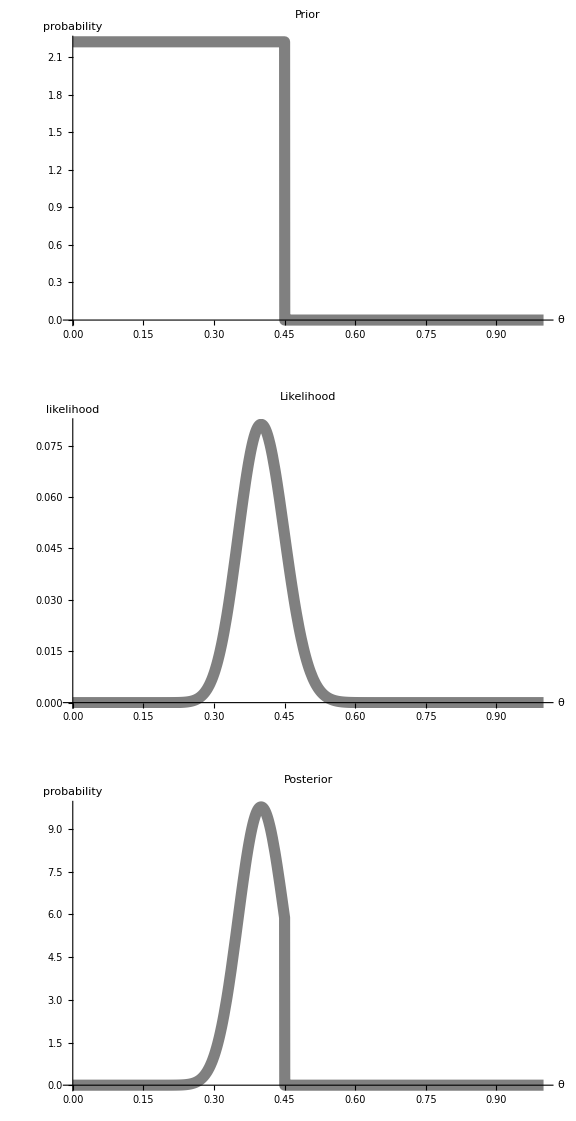

```mathematica
g1 = Plot[vPrior[θ],{θ,0,1},PlotRange->{{0,1},Full},PlotStyle->{Thickness[0.02],Gray},BaseStyle->{FontSize->16},AxesLabel->{"θ","probability"},PlotLabel->"Prior"];
g2 = Plot[vLikelihood[θ],{θ,0,1},PlotRange->{{0,1},Full},PlotStyle->{Thickness[0.02],Gray},BaseStyle->{FontSize->16},AxesLabel->{"θ","likelihood"},PlotLabel->"Likelihood"];
g3 = Plot[vPosterior[θ],{θ,0,1},PlotRange->{{0,1},Full},PlotStyle->{Thickness[0.02],Gray},BaseStyle->{FontSize->16},AxesLabel->{"θ","probability"},PlotLabel->"Posterior"];
Show[GraphicsColumn[{g1,g2,g3}],ImageSize->Large]
```